```mathematica
Clear[θ,θθ,m,r,a,Δ,ρ]
g=({{Δ/ρ^2-a^2 Sin[θ]^2/ρ^2, 0, -Δ/ρ^2(a Sin[θ]^2)+Sin[θ]^2/ρ^2 a(r^2+a^2), 0}, {0, -ρ^2/Δ, 0, 0}, {-Δ/ρ^2(a Sin[θ]^2)+Sin[θ]^2/ρ^2 a(r^2+a^2), 0, -(Δ/ρ^2(a Sin[θ]^2)^2-Sin[θ]^2/ρ^2(r^2+a^2)^2), 0}, {0, 0, 0, -ρ^2}})
```

{{Δ/ρ^2-(a^2 Sin[θ]^2)/ρ^2,0,(a (a^2+r^2) Sin[θ]^2)/ρ^2-(a Δ Sin[θ]^2)/ρ^2,0},{0,-ρ^2/Δ,0,0},{(a (a^2+r^2) Sin[θ]^2)/ρ^2-(a Δ Sin[θ]^2)/ρ^2,0,((a^2+r^2)^2 Sin[θ]^2)/ρ^2-(a^2 Δ Sin[θ]^4)/ρ^2,0},{0,0,0,-ρ^2}}

```mathematica
({{1, 0, a/(2m(m+√(m^2-a^2))), 0}}).g.({{1}, {0}, {a/(2m(m+√(m^2-a^2)))}, {0}})//.{r->m+√(m^2-a^2),ρ->√(r^2+a^2 Cos[θ]^2),Δ->r^2-2m r+a^2}//Simplify
```

{{0}}

1.74853

2.16901

{{(-4 m^2 (a^2-2 m (m+√(-a^2+m^2))) (a^2+r (-2 m+r))-a^2 (8 m^4+8 m^3 (√(-a^2+m^2)-r)-8 m^2 √(-a^2+m^2) r+r^4+2 a^2 (-2 m^2+r^2)+a^4 Cos[θ]^2) Sin[θ]^2+a^4 r (-2 m+r) Sin[θ]^4)/(4 m^2 (m+√(-a^2+m^2))^2 (r^2+a^2 Cos[θ]^2))}}

1/(4 (1+(2 √2)/3)^2 (1/18+r^2))(1/324 (-2+r) r-4 (1/9-2 (1+(2 √2)/3)) (1/9+(-2+r) r)+1/18 (-1297/162-8 ((2 √2)/3-r)+(16 √2 r)/3-r^4-2/9 (-2+r^2)))

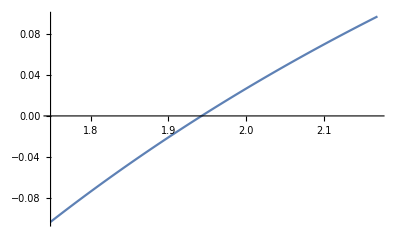

4 m^2 (a^2-2 m (m+√(-a^2+m^2))) (-1+ϵ^2)-Sin[θ]^2 (8 m^4-8 m^2 √(-a^2+m^2) √((m-a ϵ) (m+a ϵ))+a^4 (-1+ϵ^2)^2+4 a^2 m (-2 m ϵ^2-(-1+ϵ^2) √(m^2-a^2 ϵ^2))+a^4 (-1+ϵ^2) Sin[θ]^2)

```mathematica
rule={a->m/3,m->1,θ->Pi/2/2};
rMin=0.9(m+√(m^2-a^2))//.rule
rMax=1.1(m+√(m^2-a^2 Cos[θ]^2))//.rule
({{1, 0, a/(2m(m+√(m^2-a^2))), 0}}).g.({{1}, {0}, {a/(2m(m+√(m^2-a^2)))}, {0}})//.{ρ->√(r^2+a^2 Cos[θ]^2),Δ->r^2-2m r+a^2};
%//FullSimplify
%[[1,1]]//.rule
Plot[%,{r,rMin,rMax}]
```

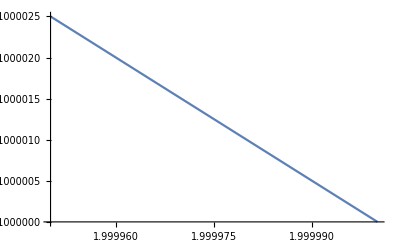

```mathematica
rule={a->m/100,m->1,θ->Pi/2};
rMin=(m+√(m^2-a^2))//.rule;
rMax=1(m+√(m^2-a^2 Cos[θ]^2))//.rule;
-Δ/(r^2+a^2 Cos[θ]^2)(a Sin[θ]^2)+Sin[θ]^2/(r^2+a^2 Cos[θ]^2)a(r^2+a^2)//.{ρ->√(r^2+a^2 Cos[θ]^2),Δ->r^2-2m r+a^2};
%//.rule;

Plot[%,{r,rMin,rMax}]
```

```mathematica
Δ/(r^2+a^2 Cos[θ]^2)(a Sin[θ]^2)^2-Sin[θ]^2/(r^2+a^2 Cos[θ]^2)(r^2+a^2)^2//.{ρ->√(r^2+a^2 Cos[θ]^2),Δ->r^2-2m r+a^2}//Simplify
Solve[%==0,r]//Simplify
```

(-(a^2+r^2)^2 Sin[θ]^2+a^2 (a^2+r (-2 m+r)) Sin[θ]^4)/(r^2+a^2 Cos[θ]^2)

$Aborted

```mathematica
-(a^2 Sin[θ]^2)/(+2 m (m+√(-a^2+m^2))-a^2(1- Cos[θ]^2))
(a^2 Sin[θ]^2)/(a^2 Sin[θ]^2-2 m (m+√(-a^2+m^2)))
1/(1-(2 m/a (m/a+√(-1+m^2/a^2)))/Sin[θ]^2)
```

-(a^2 Sin[θ]^2)/(2 m (m+√(-a^2+m^2))-a^2 (1-Cos[θ]^2))

(a^2 Sin[θ]^2)/(-2 m (m+√(-a^2+m^2))+a^2 Sin[θ]^2)

1/(1-(2 m (m/a+√(-1+m^2/a^2)) Csc[θ]^2)/a)

```mathematica
-Δ/(r^2+a^2 Cos[θ]^2)(a Sin[θ]^2)+Sin[θ]^2/(r^2+a^2 Cos[θ]^2)a(r^2+a^2)//.{ρ->√(r^2+a^2 Cos[θ]^2),Δ->r^2-2m r+a^2}//Simplify
```

(2 a m r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)

```mathematica
//.{ρ->√(r^2+a^2 Cos[θ]^2),Δ->r^2-2m r+a^2}//Simplify{ρ->√(r^2+a^2 Cos[θ]^2),Δ->r^2-2m r+a^2}//Simplify//PowerExpand
```

(-(a^2+r^2)^2 Sin[θ]^2+a^2 (a^2+r (-2 m+r)) Sin[θ]^4)/(r^2+a^2 Cos[θ]^2)

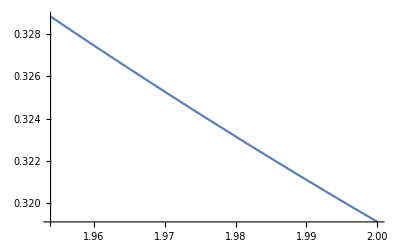

```mathematica
rule={a->0.3m,m->1,θ->Pi/2};
rMin=(m+√(m^2-a^2))//.rule;
rMax=(m+√(m^2-a^2 Cos[θ]^2))//.rule;
1/2 (-2+(4 m)/r-a^3/(m (m+√(-a^2+m^2))^2 r)+(a (r^2+(a^2 (2 m+r))/r))/(m (m+√(-a^2+m^2))))//.rule;
Plot[%,{r,rMin,rMax}]
```

```mathematica
-(1-(2m r)/(r^2+a^2 Cos[θ]^2))+(r^2+a^2+(2m r a^2 Sin[θ]^2)/(r^2+a^2 Cos[θ]^2))Sin[θ]^2 a/(2m (m+√(m^2-a^2)))-(2m r a Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)(a/(2m (m+√(m^2-a^2))))^2//.{θ->Pi/2,r->m+√(m^2-a^2)}//FullSimplify
```

(a (-a^2 (1+4 m^2)+2 a m (m+√(-a^2+m^2))+8 m^3 (m+√(-a^2+m^2))))/(2 m (m+√(-a^2+m^2))^3)